stochmatrix . Vvector = steadystatevector
-objectivefunc ∈ solution space within boundaries

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]
Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]
```

{1,0,0,0,1,1,0}

{0,1,0,1,1,1,0}

```mathematica
FindMaximum[{2v1+v4,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{2.,{v1→1.,v2→0.,v3→0.,v4→0.,b1→1.,b2→1.,b3→0.}}

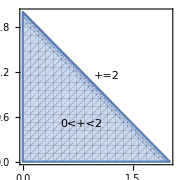

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},PlotLabels->Placed["0<+<2",{0.8,0.5}]],Plot[-+2,{,0,1.2},PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```